```mathematica
test = Import["/home/dk0r/git/comp-phys/HW_3/x-y-positionMercury.csv"];
```

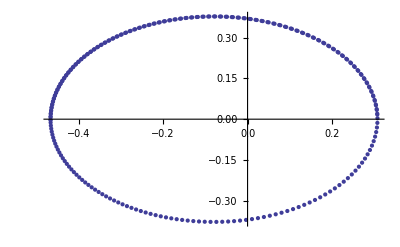

```mathematica
testplot=ListPlot[test]
```

```mathematica
Show[%59,ImageSize->Large]
```

```mathematica
btest = Import["/home/dk0r/git/comp-phys/HW_3/test/10.csv"];
```

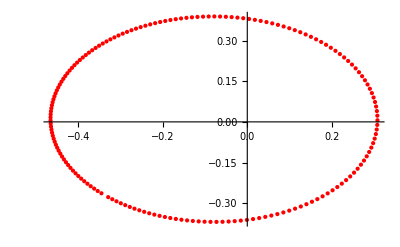

```mathematica
btestplot=ListPlot[btest, PlotStyle->Red]
```

```mathematica
Show[%58,ImageSize->Large]
```

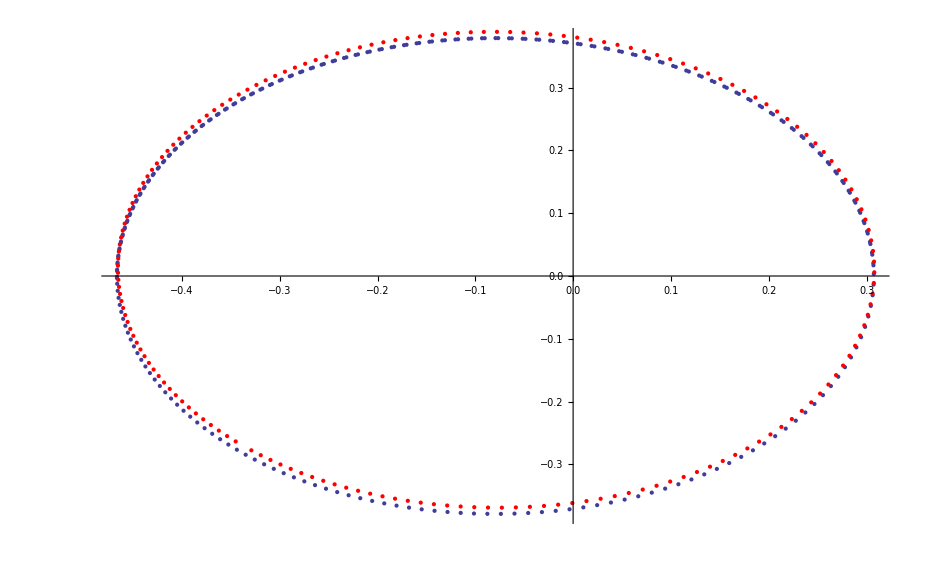

```mathematica
Show[testplot, btestplot]
```

```mathematica
atest=Import["/home/dk0r/git/comp-phys/HW_3/x-y-positionMercury.csv"];
ListPlot[atest]
```

-Graphics-

```mathematica
ctest = Import["/home/dk0r/git/comp-phys/HW_3/test/test.csv"];
```

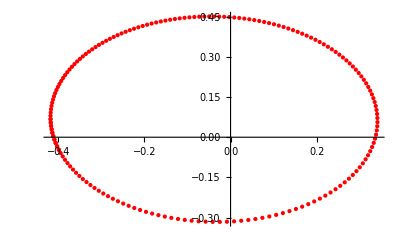

```mathematica
ctestplot = ListPlot[ctest,PlotStyle->Red]
```

```mathematica
Show[%66,ImageSize->Large]
```

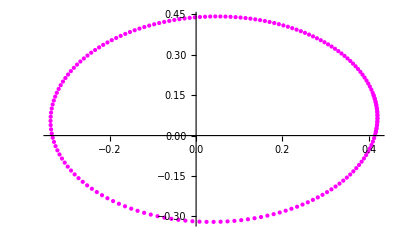

```mathematica
dtest = Import["/home/dk0r/git/comp-phys/HW_3/test/test_2.csv"];
dtestplot = ListPlot[dtest,PlotStyle->Magenta]
```

```mathematica
Show[%77,ImageSize->Large]
```

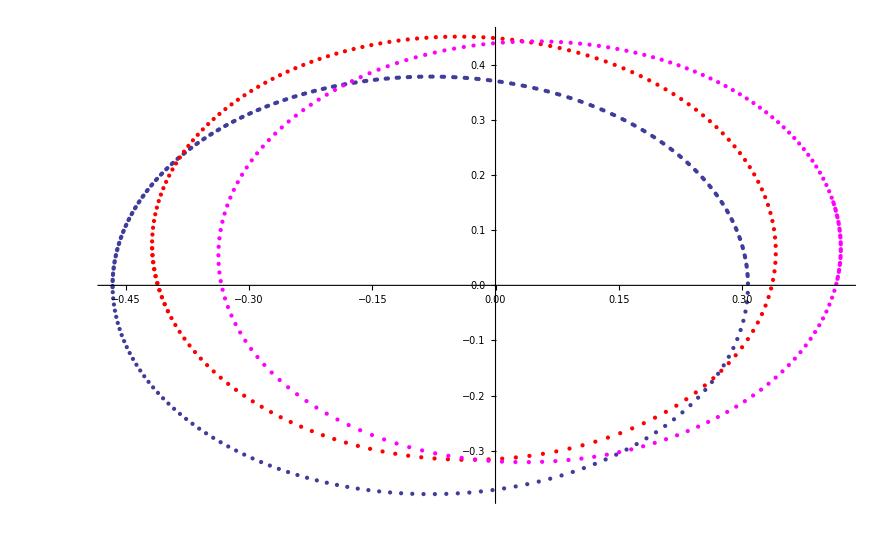

```mathematica
Show[testplot,ctestplot,dtestplot,PlotRange->Automatic]
```

```mathematica
bigEarth = Import["/home/dk0r/git/comp-phys/HW_3/x-y_position.BigEarth.csv"];
```

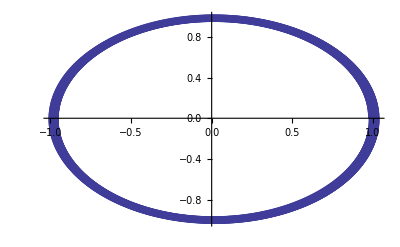

```mathematica
bigEarthPlot = ListPlot[bigEarth]
```

```mathematica
earth = Import["/home/dk0r/git/comp-phys/HW_3/x-y_position.Earth.csv"];
```

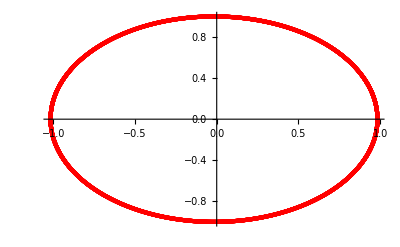

```mathematica
earthPlot = ListPlot[earth, PlotStyle->Red]
```

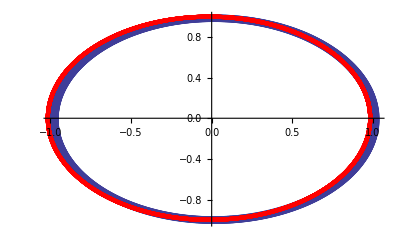

```mathematica
Show[bigEarthPlot, earthPlot]
```

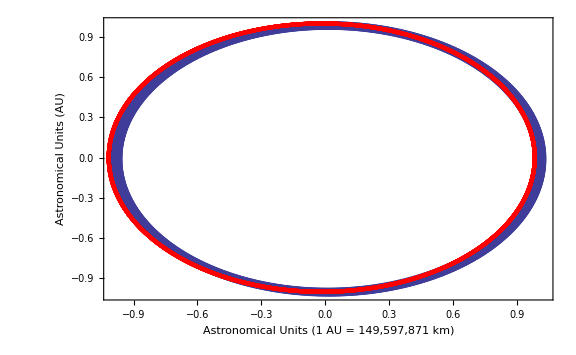

```mathematica
Show[%10,ImageSize->Large,LabelStyle->{FontSize->15},Frame->True,FrameLabel->{"Astronomical Units (1 AU = 149,597,871 km)","Astronomical Units (AU)"}]
```